### mirror baryon velocity distribution in earth frame

#### analytical definition

```mathematica
fvnorm1=Integrate[v/(√π v0 ve)ⅇ^(-(v^2+ve^2)/v0^2) (ⅇ^((2 v ve)/v0^2)-ⅇ^(-(2 cϕmax v ve)/v0^2))/.{cϕmax-> 1},{v,0,vescape - ve}]//FullSimplify

fvnorm2=Integrate[v/(√π v0 ve)ⅇ^(-(v^2+ve^2)/v0^2) (ⅇ^((2 v ve)/v0^2)-ⅇ^(-(2 cϕmax v ve)/v0^2))/.{cϕmax-> (vescape^2-ve^2-v^2)/(2 v ve)},{v,vescape - ve, vescape + ve}]//FullSimplify

fvnorm=fvnorm1+fvnorm2//FullSimplify

correctf[v_]:=(-(2 ⅇ^(-vescape^2/v0^2) vescape)/(√π v0)+Erf[vescape/v0])^-1 v/(√π v0 ve)ⅇ^(-(v^2+ve^2)/v0^2) (ⅇ^((2 v ve)/v0^2)-ⅇ^(-(2 cϕmax v ve)/v0^2))/.{cϕmax-> Which[v ≥  vescape+ve, -1, v ≤  vescape - ve, 1, True, (vescape^2-ve^2-v^2)/(2 v ve)]}
```

1/2 (((ⅇ^(-vescape^2/v0^2)-ⅇ^(-(-2 ve+vescape)^2/v0^2)) v0)/(√π ve)+Erf[vescape/v0]+Erf[(-2 ve+vescape)/v0])

1/2 ((ⅇ^(-(-2 ve+vescape)^2/v0^2) v0)/(√π ve)-(ⅇ^(-vescape^2/v0^2) (v0^2+4 ve vescape))/(√π v0 ve)+Erf[(2 ve-vescape)/v0]+Erf[vescape/v0])

-(2 ⅇ^(-vescape^2/v0^2) vescape)/(√π v0)+Erf[vescape/v0]

as we can see, the effect of vesc < ∞ is really really minimal for vesc = 544 km/s... BUT we should include it, just in case some of the tails matter for XENON in particular...

```mathematica
vsub={vescape->544, ve->233, v0->220};
correctf[v]/.vsub/.{v->300}//N
```

0.00302018

#### CDM vesc demo

General::munfl: Exp[-206612.] is too small to represent as a normalized machine number; precision may be lost.

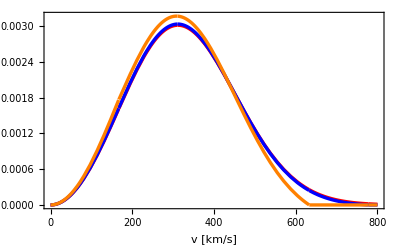

```mathematica
vsub={vescape->544, ve->233, v0->220};

Plot[Evaluate[{
correctf[v]/.{vescape->100000, ve->233, v0->220}
,
correctf[v]/.vsub
,
correctf[v]/.{vescape->400, ve->233, v0->220}
}],{v,0,800}, PlotRange->All, BaseStyle->{FontSize->14, FontFamily->"Times New Roman"},  Frame->True,  FrameLabel->{"v [km/s]", None}, PlotStyle->(Directive[#, Thickness->0.006]&/@{Red, Blue, Orange})]
```

#### disk

General::munfl: Exp[-1111.11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

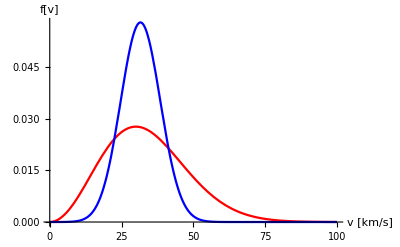

```mathematica
Plot[
Evaluate[{
correctf[v]/.{vescape->1000, ve->0.0001, v0->30}
,
correctf[v]/.{vescape->1000, ve->30, v0->10}
}]
,{v,0,100},AxesLabel->{"v [km/s]", "f[v]"}, PlotStyle->{Red,Blue}, AxesOrigin->{0,0}, FrameTicks->Automatic]
```

### mbar and Y as function of foverv

```mathematica
fovervvsΛratiotable = {{2.,1.1665290395761165},{2.2,1.1914996773310675},{2.4,1.214762528992457},{2.6,1.2365631480518564},{2.8,1.2570960200157553},{3.,1.2765180070092417},{3.2,1.2949576057390506},{3.4,1.312521499493589},{3.6,1.3292993057956153},{3.8,1.3453670880289161},{4.,1.360790000174377},{4.2,1.3756243107954398},{4.4,1.389918974252263},{4.6,1.403716866175517},{4.8,1.4170557662586254},{5.,1.4299691483087287},{5.2,1.4424868214721513},{5.4,1.4546354552558614},{5.6,1.4664390128839375},{5.8,1.4779191116628334},{6.,1.4890953247181091},{6.2,1.4999854352588131},{6.4,1.510605652114562},{6.6,1.5209707934588088},{6.8,1.5310944442272607},{7.,1.5409890916538365},{7.2,1.5506662424989575},{7.4,1.5601365248786914},{7.6,1.5694097770756883},{7.8,1.5784951252922297},{8.,1.5874010519681994},{8.2,1.5961354560143224},{8.4,1.6047057060897616},{8.6,1.613118687872552},{8.8,1.6213808461231134},{9.,1.6294982222188463},{9.2,1.637476487736522},{9.4,1.6453209745748916},{9.6,1.6530367020394723},{9.8,1.6606284012523553},{10.,1.6681005372000588}}

Λratio[foverv_]:=Interpolation[fovervvsΛratiotable,InterpolationOrder->1][foverv]

mHGeV[foverv_]:=Λratio[foverv]*0.93
```

{{2.,1.16653},{2.2,1.1915},{2.4,1.21476},{2.6,1.23656},{2.8,1.2571},{3.,1.27652},{3.2,1.29496},{3.4,1.31252},{3.6,1.3293},{3.8,1.34537},{4.,1.36079},{4.2,1.37562},{4.4,1.38992},{4.6,1.40372},{4.8,1.41706},{5.,1.42997},{5.2,1.44249},{5.4,1.45464},{5.6,1.46644},{5.8,1.47792},{6.,1.4891},{6.2,1.49999},{6.4,1.51061},{6.6,1.52097},{6.8,1.53109},{7.,1.54099},{7.2,1.55067},{7.4,1.56014},{7.6,1.56941},{7.8,1.5785},{8.,1.5874},{8.2,1.59614},{8.4,1.60471},{8.6,1.61312},{8.8,1.62138},{9.,1.6295},{9.2,1.63748},{9.4,1.64532},{9.6,1.65304},{9.8,1.66063},{10.,1.6681}}

```mathematica
"what is mbar for full ionization?"
analyticalmbar=(mH nH + mHe nHe)/(nH + nHe + ne)
analyticalmbarfullion=analyticalmbar/.{ne-> 2 nHe + nH}//FullSimplify
Solve[(mHe nHe)/(nH mH + mHe nHe)==Ylocal,nHe][[1]]
analyticalmbarfullion=%%/.%/.{mHe->4mH}//FullSimplify
```

what is mbar for full ionization?

(mH nH+mHe nHe)/(ne+nH+nHe)

(mH nH+mHe nHe)/(2 nH+3 nHe)

{nHe→-(mH nH Ylocal)/(mHe (-1+Ylocal))}

(4 mH)/(8-5 Ylocal)

```mathematica
mbarGeVfullionization[foverv_,Y_]:=analyticalmbarfullion/.{mH-> mHGeV[foverv],Ylocal->Y}
```

```mathematica
(*v0 for E, He in galactic system frame, but not earth frame*)
v0kmsHeHalo[foverv_,Y_]:= 220 √(mbarGeVfullionization[foverv,Y]/(4 mHGeV[foverv])) 
v0kmsHeDisk[foverv_,Y_]:= 20 √(mbarGeVfullionization[foverv,Y]/(4 mHGeV[foverv])) 

v0kmsEHalo[foverv_,Y_]:= 220 √(mbarGeVfullionization[foverv,Y]/(foverv 0.511*10^-3)) 
v0kmsEDisk[foverv_,Y_]:= 20 √(mbarGeVfullionization[foverv,Y]/(foverv 0.511*10^-3))
```

```mathematica
vEarthkmsDisk=30;
vEarthkmsHalo=220;

vescapehuge=10000000;
```

### cases to consider for calculation

f/v = 3 or 5, with Y = 0.1, 0.75, 1
--> 6 choices of (foverv, Y)

each for disk and halo
always set rho_mirrorbaryons = 5% * DM

mirror helium and electron masses

{4.74865,0.001533}

mbar (do not need, just for demonstration. use the below functions to get v0 for the different species

1.58288

mirror helium and electron v0 for DISK case

{642.663,11.547}

mirror helium and electron v0 for HALO case

{7069.29,127.017}

mirror helium density depends on Y

Y ρmirrorbaryons

General::munfl: Exp[-7.5×10^11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.42122×10^8] is too small to represent as a normalized machine number; precision may be lost.

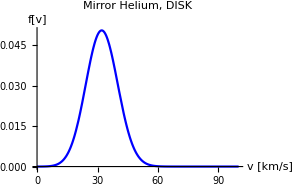
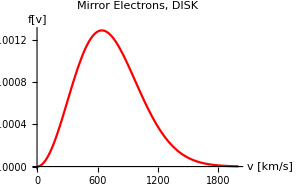

General::munfl: Exp[-6.19835×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.001×10^6] is too small to represent as a normalized machine number; precision may be lost.

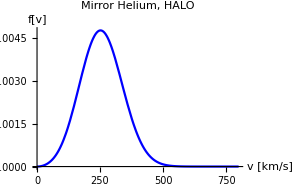
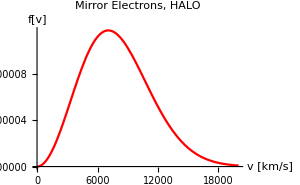

```mathematica
currentfoverv=3;
currentY =1;

"mirror helium and electron masses"
{4*mHGeV[currentfoverv], currentfoverv*0.511*^-3  }

"mbar (do not need, just for demonstration. use the below functions to get v0 for the different species"
mbarGeVfullionization[currentfoverv, currentY]


"mirror helium and electron v0 for DISK case"
{v0kmsEDisk[currentfoverv,currentY],v0kmsHeDisk[currentfoverv,currentY]}
"mirror helium and electron v0 for HALO case"
{v0kmsEHalo[currentfoverv,currentY],v0kmsHeHalo[currentfoverv,currentY]}


"mirror helium density depends on Y"
ρMirrorHelium = Y ρmirrorbaryons




{Plot[
Evaluate[{
correctf[v]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsHeDisk[currentfoverv,currentY]}
}]
,{v,0,100},AxesLabel->{"v [km/s]", "f[v]"},PlotRange->All, PlotStyle->Blue, AxesOrigin->{0,0}, FrameTicks->Automatic, ImageSize->300, PlotLabel->"Mirror Helium, DISK"]
,
Plot[
Evaluate[{
correctf[v]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsEDisk[currentfoverv,currentY]}
}]
,{v,0,2000},AxesLabel->{"v [km/s]", "f[v]"}, PlotRange->All,PlotStyle->Red, AxesOrigin->{0,0}, FrameTicks->Automatic, ImageSize->300, PlotLabel->"Mirror Electrons, DISK"]
}



{Plot[
Evaluate[{
correctf[v]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsHeHalo[currentfoverv,currentY]}
}]
,{v,0,800},AxesLabel->{"v [km/s]", "f[v]"},PlotRange->All, PlotStyle->Blue, AxesOrigin->{0,0}, FrameTicks->Automatic, ImageSize->300, PlotLabel->"Mirror Helium, HALO"]
,
Plot[
Evaluate[{
correctf[v]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsEHalo[currentfoverv,currentY]}
}]
,{v,0,20000},AxesLabel->{"v [km/s]", "f[v]"}, PlotRange->All,PlotStyle->Red, AxesOrigin->{0,0}, FrameTicks->Automatic, ImageSize->300, PlotLabel->"Mirror Electrons, HALO"]
}
```